# MGroups

## Finite Group Theory in Mathematica

Naman Taggar  <namantaggar [dot] 11 [at] gmail [dot] com>

MGroups is a Mathematica package that implements a part of finite Group Theory. It facilitates studying group operations, order and inverses of the group elements, Cayley tables, (ordinary and normal) subgroup structures of a group, group morphisms and more, easily and quickly. MGroups is licensed under the MIT Open-Source License.

## 1. Preface

In MGroups, groups are defined in the form of “Associations” that are the Mathematica version of mappings. Quite literally, a group in this package is nothing but its Cayley Table. For example, to define the Z_2 group, all that is needed is to define

How 0 operates with 0,

How 0 operates with 1,

How 1 operates with 0, and

How 1 operates with 1.

In Mathematica, Associations are of the form

```mathematica
<|a->b,c->d,e->f|>;
```

which means that a maps to b, c maps to d, and e maps to f. Now, it is only appropriate to see how Z_2 will be defined in such a way:—

```mathematica
Subscript[Z, 2]=<|0-><|0->0,1->1|>,1-><|0->1,1->0|>|>;
```

... which is nothing but nested Associations. Now, if we need to see what is 0*0 in Z_2, we can type

```mathematica
Subscript[Z, 2][0][0]
```

0

to get the required output. Similarly, other complex groups are also defined.

## 2. Installation

To install the package, you can open any Mathematica notebook and run the following command:

```mathematica
PacletInstall["Taggar/MGroups"]
```

PacletObject[…]

Then, whenever you need to use MGroups in a Mathematica notebook, type

```mathematica
<<Taggar`MGroups`
```

which will call the package. Now type

```mathematica
Subscript[Z, 2]=MAdditiveGroup[2]
```

MGroup[…]

If you get the same output as above, then congratulations — you have successfully installed MGroups!

## 3. Introduction

This documentation covers each aspect of the package, from basic to advanced. We define a group first:—

Definition (Group). A group is a non-empty set in Mathematics, elements of which follow 4 properties namely closure, associativity, existence of identity, and existence of inverses under a certain binary operation.

### Available Groups

This package provides the groups as tabulated below.

Group | Description
MAdditiveGroup | Z_n: The group {0, 1, ..., n-1} formed 
under addition modulo n.
MMultiplicativeGroup | U_n: The group {0<=x<n: gcd(x,n)==1} formed
under multiplication modulo n.
MDihedralGroup | D_n: The group of symmetries of a regular 
polygon formed under their composition.
MPermutationsGroup | S_A: The group of  permutations of a non-empty
               set formed under their composition.
MKlein4Group & MQuaternionGroup | Klein's 4 Group and the Quaternion Group.
MEDP | The External Direct Product of given groups.

They can be called by their respective function names.

### Defining a Group

In addition to the in-build functions shown above, groups can be freely formed with the following command giving a domain and a bianry operation:—

```mathematica
domain:={0}
function[x_,y_]:=x+y
G=FormMGroup[domain,function]
```

MGroup[…]

### Basic Operations

Define a group using one of the functions as shown below.

```mathematica
Subscript[D, 4]=MDihedralGroup[4]
```

MGroup[…]

and check the domain of this group:—

```mathematica
MGroupDomain[Subscript[D, 4]]
```

{r0,r1,r2,r3,s0,s1,s2,s3}

Group operations can be applied just by indexing those elements through the objects.

```mathematica
Subscript[D, 4]["r2"]["s3"]
```

s1

```mathematica
Subscript[D, 4]["s1"]["s1"]
```

r0

Trying some other group:—

```mathematica
MMultiplicativeGroup[13][3][4]
```

12

which is 3 × 4 (mod 13). Doing something more exciting...

```mathematica
MDihedralGroup[240]["s60"]["r190"]
```

s10

which is the composition of the 191st rotation and reflection about the 61st axis, in the Dihedral group of order 480.

External Direct Products can be formed as follows:—

```mathematica
Subscript[Z, 2]:=MAdditiveGroup[2]
MEDP[Subscript[Z, 2],Subscript[Z, 2]]
```

MGroup[…]

A more complicated EDP:

```mathematica
Subscript[E, 1]=MEDP[
MAdditiveGroup[6],
MMultiplicativeGroup[10],
 MQuaternionGroup
]
```

MGroup[…]

The order of this group is 192 will is equal to 6×4×8 as we expected. Click on the + icon to see that here identity of this group is {0,1,1}.

In EDPs, elements are wrapped with MTuple and operations are done component-wise. For example,

```mathematica
Subscript[x, 1]:=MTuple[{5,3,"-j"}]
Subscript[x, 2]:=MTuple[{4,7,"k"}]
Subscript[E, 1][Subscript[x, 1]][Subscript[x, 2]]
```

(3, 1, i)

### Group Properties

You can check whether a group is abelian or cyclic using AbelianQ or CyclicQ commands respectively.

```mathematica
MAdditiveGroup[10]//MAbelianQ
```

True

```mathematica
MKlein4Group//MAbelianQ
```

True

```mathematica
MDihedralGroup[3]//MCyclicQ
```

False

```mathematica
MEDP[MAdditiveGroup[6],MAdditiveGroup[7]] // MCyclicQ
```

True

### Cayley Tables

Complete Cayley Tables can be printed for any group using CayleyTable command.

```mathematica
MCayleyTable[MQuaternionGroup]
```

| 1 | -1 | i | -i | j | -j | k | -k
1 | 1 | -1 | i | -i | j | -j | k | -k
-1 | -1 | 1 | -i | i | -j | j | -k | k
i | i | -i | -1 | 1 | k | -k | -j | j
-i | -i | i | 1 | -1 | -k | k | j | -j
j | j | -j | -k | k | -1 | 1 | i | -i
-j | -j | j | k | -k | 1 | -1 | -i | i
k | k | -k | j | -j | -i | i | -1 | 1
-k | -k | k | -j | j | i | -i | 1 | -1

or for an EDP:—

```mathematica
MEDP[MAdditiveGroup[2],MMultiplicativeGroup[3]]// MCayleyTable
```

| (0, 1) | (0, 2) | (1, 1) | (1, 2)
(0, 1) | (0, 1) | (0, 2) | (1, 1) | (1, 2)
(0, 2) | (0, 2) | (0, 1) | (1, 2) | (1, 1)
(1, 1) | (1, 1) | (1, 2) | (0, 1) | (0, 2)
(1, 2) | (1, 2) | (1, 1) | (0, 2) | (0, 1)

### Orders and Inverses

Table of Orders and Inverses for a group can also be printed as follows:—

```mathematica
MInversesTable[MDihedralGroup[6]]
```

x | x^-1 | |x|=|x^-1|
r0 | r0 | 1
r1 | r5 | 6
r2 | r4 | 3
r3 | r3 | 2
r4 | r2 | 3
r5 | r1 | 6
s0 | s0 | 2
s1 | s1 | 2
s2 | s2 | 2
s3 | s3 | 2
s4 | s4 | 2
s5 | s5 | 2

```mathematica
MElementInverse[MAdditiveGroup[4],2]
```

2

```mathematica
MInversesTable[MPermutationsGroup[3]]
```

x | x^-1 | |x|=|x^-1|
(1) | (1) | 1
(23) | (23) | 2
(12) | (12) | 2
(123) | (132) | 3
(132) | (123) | 3
(13) | (13) | 2

## 4. Subgroups

We define a subgroup.

Definition (Subgroup of a group). A subset H⊆G  is said to be a subgroup of the group G if it forms a group itself under the operation of G.

We can check this in MGroups as follows:—

```mathematica
Subscript[Z, 20]:=MAdditiveGroup[20] (* {0, 1, ..., 19} *)
H:=Table[2i,{i,0,9}] (* {0, 2, ..., 18} *)
MSubgroupQ[Subscript[Z, 20],H]
```

True

```mathematica
MSubgroupQ[MDihedralGroup[10],{"s3","r0","r2","r3"}]
```

False

All subgroups can be obtained using

```mathematica
MSubgroups[MDihedralGroup[5]]
```

Subgroup | Generated by
{r0} | {r0}
{r0,r1,r2,r3,r4} | {r1}
{r0,s0} | {s0}
{r0,s1} | {s1}
{r0,s2} | {s2}
{r0,s3} | {s3}
{r0,s4} | {s4}
{r0,r1,r2,r3,r4,s0,s1,s2,s3,s4} | {r1,s0}

The package generates subgroups by each subset of cardinality less than or equal to 3. However, in some groups, only at most 2 elements are needed to exhibit all subgroups. Hence, for quicker outputs, this number can be set using CombinationsLimit option in commands related to subgroups generation. For example, compare the difference while calculating all 30 subgroups of S_4:

```mathematica
Table[AbsoluteTiming[Length@MSubgroups[MPermutationsGroup[4],CombinationsLimit->i][[1]]],{i,2,3}]
```

{{0.253327,30},{2.21802,30}}

List the cyclic subgroups of U_30:—

```mathematica
Subscript[U, 30]=MMultiplicativeGroup[30]
```

MGroup[…]

```mathematica
Select[
First@MSubgroups[Subscript[U, 30]],
MCyclicQ[Subscript[U, 30],#[[1]]]&
][[All,1]]
```

{{1},{1,7,13,19},{1,11},{1,17,19,23},{1,19},{1,29}}

## 5. Subgroup Lattices

Most interestingly, you can also see subgroup lattices of groups using this package. For example, let us see the subgroup lattice of Z_4.

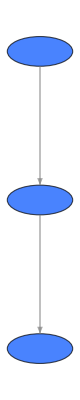

```mathematica
MAdditiveGroup[4]//MSubgroupLattice
```

Here, the top most node is the group Z_4 itself, at the bottom we have {0}, and in the middle we must have {0, 2}. Hover on the nodes to see details about each subgroup. Let us proceed further and see something more exciting:—

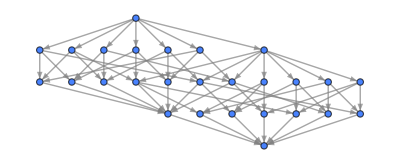

```mathematica
MSubgroupLattice[MMultiplicativeGroup[40]]
```

Beautiful! Subgroup Lattices of some Dihedral Groups:—

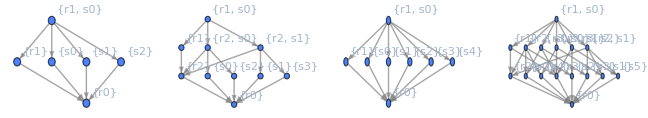

```mathematica
GraphicsRow@Table[MSubgroupLattice[MDihedralGroup[i],MShowInfo->"Generators"],{i,3,6}]
```

or D_8 with normal subgroups highlighted and each subgroup labelled:

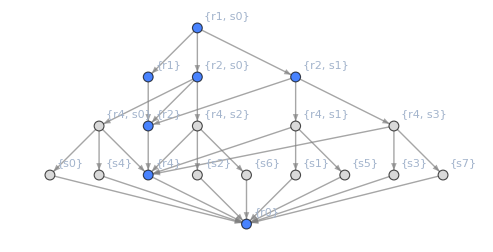

```mathematica
MSubgroupLattice[MDihedralGroup[8],MHighlight->MNormalSubgroupQ,MShowInfo->"Generators"]
```

Symmetric group S_3:—

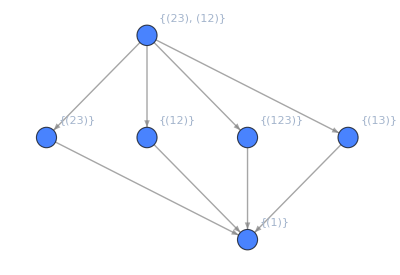

```mathematica
MSubgroupLattice[MPermutationsGroup[3],MShowInfo->"Generators"]
```

or S_4:

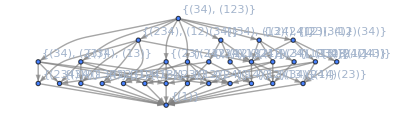

```mathematica
MSubgroupLattice[MPermutationsGroup[4],MShowInfo->"Generators"]
```

### Some EDPs

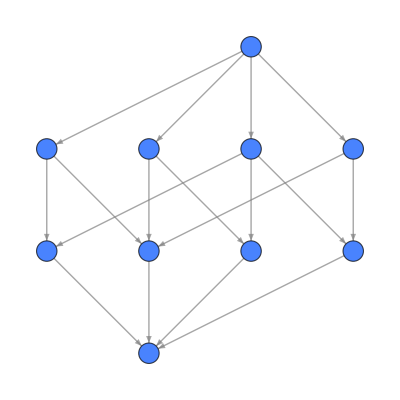

```mathematica
MEDP[MAdditiveGroup[6],MAdditiveGroup[2]]//MSubgroupLattice
```

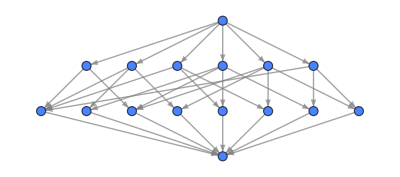

```mathematica
MEDP[MDihedralGroup[3],MAdditiveGroup[2]]//MSubgroupLattice
```

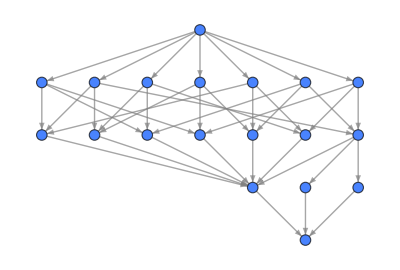

```mathematica
MEDP[MQuaternionGroup,MAdditiveGroup[2]]//MSubgroupLattice
```

## 6. Cosets and Normal Subgroups

Definition (Coset). If H is a subgroup of G, then for some a in G, the set {a h: h∈H} is called the left coset of H in G containing a. Subsequently, corresponding right coset is the set {h a: h∈H}.

You can define cosets in this package as follows:—

```mathematica
Subscript[E, 2]=MEDP[MMultiplicativeGroup[8],MKlein4Group]
Subscript[H, 2]={MTuple[{1,"e"}],MTuple[{1,"c"}]};(* any one subgroup *)
```

MGroup[…]

```mathematica
MCoset[Subscript[E, 2],Subscript[H, 2],MTuple[{3,"b"}],"l"]
```

{(3, b),(3, a)}

```mathematica
MCoset[Subscript[E, 2],Subscript[H, 2],MTuple[{3,"b"}],"r"]
```

{(3, b),(3, a)}

Both are equal.

Definition (Normal Subgroup of a group). A subgroup H of G is said to be normal in G if the left coset by every element is equal to the right counterpart.

To find normal subgroups of a group:—

```mathematica
MNormalSubgroups@MQuaternionGroup
```

Subgroup | Generated by
{1} | {1}
{-1,1} | {-1}
{-1,1,-i,i} | {i}
{-1,1,-j,j} | {j}
{-1,1,-k,k} | {k}
{-1,1,-i,i,-j,j,-k,k} | {i,j}

## 7. Morphisms

Definition (Group Homomorphism). A map ϕ from G_1 to G_2 is said to be a homomorphism, if and only if it is operation preserving, i.e., if ϕ(xy)=ϕ(x)ϕ(y) ∀x,y∈G_1.

To define a Group Homomorphism, you need to define the domain, the codomain, and the map’s definition. It can be done as follows:—

```mathematica
ϕ=MHomomorphism[
MAdditiveGroup[20], (* domain *)
MAdditiveGroup[2], (* co-domain *)
Mod[#,2]& (* definition in the form of a function *)
]
```

MMorphism[…]

We can see that the kernel of phi is {0,2,...,18} by clicking on the + icon, or using the MMorphismKernel command.

```mathematica
MMorphismKernel[ϕ]
```

{0,2,4,6,8,10,12,14,16,18}

Definition (Group Isomorphism). A homomorphism ϕ is said to be an isomorphism, if and only if it is one-one.

```mathematica
MIsomorphism[
MAdditiveGroup[3],
MAdditiveGroup[3],
#&
]
```

MMorphism[…]

Definition (Group Automorphism). An isomorphism from a group to itself is said to be an automorphism.

```mathematica
MAutomorphism[
MAdditiveGroup[3],
#&
]
```

MMorphism[…]

Definition (Inner Automorphism). An inner automorphism is an automorphism that is induced by a group element a, with the definition x ⟶ a x a^-1.

```mathematica
MInnerAutomorphism[MDihedralGroup[4],"s3"]
```

MMorphism[…]

## A. Copyright

Github Repository: ["https://github.com/zplus11/MGroups.git"](https://github.com/zplus11/MGroups).

Copyright (c) 2024–25 Naman Taggar
This package is licensed under the MIT Open-Source license. See LICENSE file for more details.